```mathematica
Remove["Global`*"];
fd=((2/L)*(1-(d/L)));
fr =((2/H)*(1-(r/H)));
a={d∈Reals,r∈Reals,w∈Reals,H∈Reals,L∈Reals, L>H>w>0,w>r>0, w>d>0};

I1=Simplify[Integrate[Integrate[fd*fr,{d,0,Sqrt[w^2-r^2]},Assumptions->a],{r,0,w},Assumptions->a],a];

D1=Simplify[Dt[I1,w,Constants -> {L, H}],a];
CDF1 = I1
PDF1 = D1
```

(w^2 (6 H L π-8 (H+L) w+3 w^2))/(6 H^2 L^2)

(2 w (H L π-2 H w-2 L w+w^2))/(H^2 L^2)

```mathematica
b ={d∈Reals,r∈Reals,w∈Reals,H∈Reals,L∈Reals, L>H,w>H>d >0, w>r>0,w>d>0, H> 0, L> 0, L > w};

I2=Apart[Simplify[Integrate[Integrate[fd*fr,{d,Sqrt[H^2-r^2],Sqrt[w^2-r^2]},Assumptions->b],{r,0,H},Assumptions->b]]];
D2=FullSimplify[Dt[I2,w,Constants -> {L, H}],b];

CDF2 = FullSimplify[I2+ Function[w, Evaluate[CDF1]][H],b]
PDF2 = D2
(* NOTE! we can replace ArcTan by noting that ArcTan[H/(√(-H^2+w^2))] = ArcSin[H/w] *)
```

(H^4+8 L w^2 (-w+√(-H^2+w^2))+H^2 (-6 w^2+4 L √(-H^2+w^2))+12 H L w^2 ArcTan[H/(√(-H^2+w^2))])/(6 H^2 L^2)

-(2 w (H^2+2 L (w-√(-H^2+w^2))-2 H L ArcTan[H/(√(-H^2+w^2))]))/(H^2 L^2)

```mathematica
c = {d∈Reals,r∈Reals,w∈Reals,H∈Reals,L∈Reals,w>L>d>H>r>0,w>Sqrt[w^2-L^2],H>Sqrt[w^2-L^2],H>0, L>0 , w > H, w > L};

I3=Integrate[Integrate[fd*fr,{d, L, Sqrt[w^2-r^2]},Assumptions->c],{r, 0, Sqrt[w^2-L^2]},Assumptions->c];
D3=Simplify[Dt[I3,w,Constants -> {L, H}],c];
CDF3 = FullSimplify[I2-I3  +  1 - Function[w, Evaluate[I2 - I3]][Sqrt[H^2 + L^2]],c] 
PDF3 = FullSimplify[D2-D3  , c]
```

1/(6 H^2 L^2)(H^4+L^4+4 H √(-L^2+w^2) (L^2+2 w^2)+H^2 (-6 w^2+4 L √(-H^2+w^2))+w^2 (-6 L^2-3 w^2+8 L √(-H^2+w^2))+12 H L w^2 (-ArcCot[L/(√(-L^2+w^2))]+ArcTan[H/(√(-H^2+w^2))]))

-(2 w (H^2+L^2+w^2-2 L √(-H^2+w^2)-2 H √(-L^2+w^2)+2 H L (ArcCot[L/(√(-L^2+w^2))]-ArcTan[H/(√(-H^2+w^2))])))/(H^2 L^2)

```mathematica
CForm[Evaluate[CDF1]]
```

(Power(w,2)*(6*H*L*Pi - 8*(H + L)*w + 3*Power(w,2)))/(6.*Power(H,2)*Power(L,2))

```mathematica
CForm[Evaluate[CDF2]]
```

(Power(H,4) + 8*L*Power(w,2)*(-w + Sqrt(-Power(H,2) + Power(w,2))) + 
     Power(H,2)*(-6*Power(w,2) + 4*L*Sqrt(-Power(H,2) + Power(w,2))) + 
     12*H*L*Power(w,2)*ArcTan(H/Sqrt(-Power(H,2) + Power(w,2))))/(6.*Power(H,2)*Power(L,2))

```mathematica
CForm[Evaluate[CDF3]]
```

(Power(H,4) + Power(L,4) + 4*H*Sqrt(-Power(L,2) + Power(w,2))*(Power(L,2) + 2*Power(w,2)) + 
     Power(H,2)*(-6*Power(w,2) + 4*L*Sqrt(-Power(H,2) + Power(w,2))) + 
     Power(w,2)*(-6*Power(L,2) - 3*Power(w,2) + 8*L*Sqrt(-Power(H,2) + Power(w,2))) + 
     12*H*L*Power(w,2)*(-ArcCot(L/Sqrt(-Power(L,2) + Power(w,2))) + 
        ArcTan(H/Sqrt(-Power(H,2) + Power(w,2)))))/(6.*Power(H,2)*Power(L,2))

```mathematica
TeXForm[Evaluate[CDF1]]
```

\frac{w^2 \left(-8 w (H+L)+6 \pi  H L+3 w^2\right)}{6 H^2 L^2}

```mathematica
TeXForm[Evaluate[CDF2]]
```

\frac{H^4+H^2 \left(4 L \sqrt{w^2-H^2}-6 w^2\right)+8 L w^2 \left(\sqrt{w^2-H^2}-w\right)+12
   H L w^2 \tan ^{-1}\left(\frac{H}{\sqrt{w^2-H^2}}\right)}{6 H^2 L^2}

```mathematica
TeXForm[Evaluate[CDF3]]
```

\frac{H^4+w^2 \left(8 L \sqrt{w^2-H^2}-6 L^2-3 w^2\right)+12 H L w^2 \left(\tan
   ^{-1}\left(\frac{H}{\sqrt{w^2-H^2}}\right)-\cot
   ^{-1}\left(\frac{L}{\sqrt{w^2-L^2}}\right)\right)+H^2 \left(4 L \sqrt{w^2-H^2}-6
   w^2\right)+4 H \sqrt{w^2-L^2} \left(L^2+2 w^2\right)+L^4}{6 H^2 L^2}

```mathematica
TeXForm[Evaluate[PDF1]]
```

\frac{2 w \left(\pi  H L-2 H w-2 L w+w^2\right)}{H^2 L^2}

```mathematica
TeXForm[Evaluate[PDF2]]
```

-\frac{2 w \left(2 L \left(w-\sqrt{w^2-H^2}\right)-2 H L \tan
   ^{-1}\left(\frac{H}{\sqrt{w^2-H^2}}\right)+H^2\right)}{H^2 L^2}

```mathematica
TeXForm[Evaluate[PDF3]]
```

-\frac{2 w \left(2 H L \left(\cot ^{-1}\left(\frac{L}{\sqrt{w^2-L^2}}\right)-\tan
   ^{-1}\left(\frac{H}{\sqrt{w^2-H^2}}\right)\right)-2 L \sqrt{w^2-H^2}+H^2-2 H
   \sqrt{w^2-L^2}+L^2+w^2\right)}{H^2 L^2}

1

1

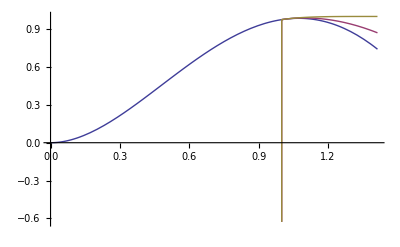

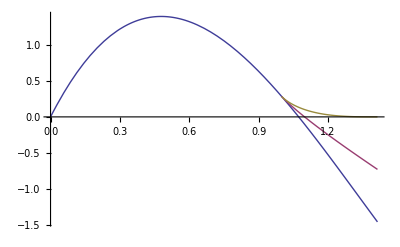

```mathematica
H=1
L=1
Plot[{CDF1,CDF2,CDF3},{w,0,Sqrt[L^2+H^2]}]
Plot[{PDF1,PDF2,PDF3},{w,0,Sqrt[L^2+H^2]}]
```

3

4

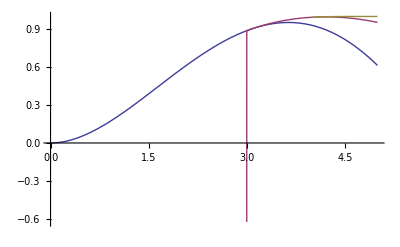

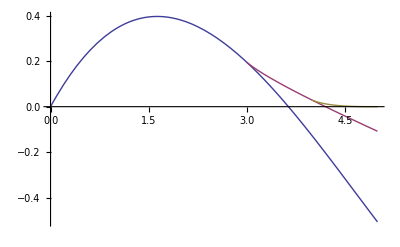

```mathematica
H=3
L=4
Plot[{CDF1,CDF2,CDF3},{w,0,Sqrt[L^2+H^2]}]
Plot[{PDF1,PDF2,PDF3},{w,0,Sqrt[L^2+H^2]}]
```

5

12

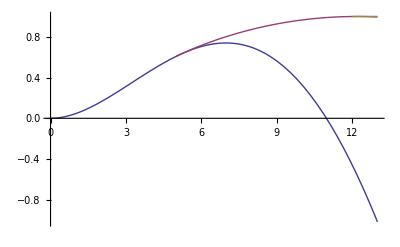

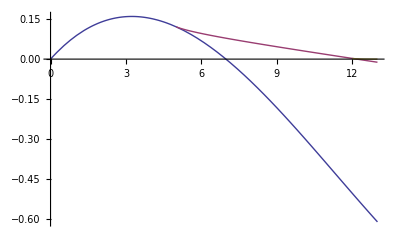

```mathematica
H=5
L=12
Plot[{CDF1,CDF2,CDF3},{w,0,Sqrt[L^2+H^2]}]
Plot[{PDF1,PDF2,PDF3},{w,0,Sqrt[L^2+H^2]}]
```